### Ej/Ec ratio

```mathematica
h=1.05457182 10^-34*2Pi;(*km m^2 /s*)
ecoul=1.60217663 10^-19;(* coulombs*)
ic=0.3;(*30 A/cm^2 = 0.3 A/mm^2*)
cap=5 10^-8;(*50 fF/um^2 = 50 10^6  10^-15 F/mm^2 = 5 10^-8 F/mm^2*)
dx=.;(*mm*)
dy=dx;(*mm*)
Ej=h/(2ecoul)ic/(2 Pi)dx dy 10^-6;(*Josephson energy*)
Ec=ecoul^2/(2 cap dx dy)10^6;
EjEcRatio[dx_]=Ej/Ec
```

384.624 dx^4

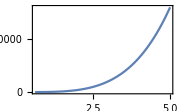

```mathematica
Plot[EjEcRatio[dx],{dx,0.6,5},FrameLabel->{"Square junction width in μm","E_J/E_C"},Frame->True,ImageSize->Small]
```

### Inductance estimation of λ

```mathematica
(*https://chemandy.com/calculators/flat-wire-inductor-calculator.htm*)
```

```mathematica
phi0=h/(2ecoul);
```

```mathematica
LL[l_,w_,t_]=2 10^-3 l (Log[(2 l)/(w+t)]+0.5+0.2235((w+t)/l)) 10^-9;(*uH*)
L[l_,w_,t_]=LL[10^-4 l,10^-4 w,10^-4 t];
Ic[w_]=ic (w /1000)^2;
λ[l_,w_,t_]=2 π L[l,w,t] Ic[w]/phi0;
```

```mathematica
Ic[10]
```

0.00003

```mathematica
Manipulate[Plot[λ[l,w,t],{w,1,10}],{{l,1000},100,20000},{{t,0.1},0.05,0.2}]
```

```mathematica
Ic[8]*10^3
```

0.0192

### Mutual inductance

```mathematica
f[x_,y_,z_]:=((y^2 z^2)/4-y^4/24-z^4/24)x Log[(x+√(x^2+y^2+z^2))/(√(y^2+z^2))]+((x^2 z^2)/4-x^4/24-z^4/24)y Log[(y+√(x^2+y^2+z^2))/(√(x^2+z^2))]+((x^2 y^2)/4-x^4/24-y^4/24)z Log[(z+√(x^2+y^2+z^2))/(√(x^2+y^2))]+1/60(x^4+y^4+z^4-3 x^2 y^2-3 y^2 z^2-3 z^2 x^2)√(x^2+y^2+z^2)-(x y z^3)/6 ArcTan[(x y)/(z √(x^2+y^2+z^2))]-(x y^3 z)/6 ArcTan[(x z)/(y √(x^2+y^2+z^2))]-(x^3 y z)/6 ArcTan[(y z)/(x √(x^2+y^2+z^2))]
```

```mathematica
c=.;
xx={ee-a,ee+d-a,ee+d,ee};
yy={pp-b,pp+c-b,pp+c,pp};
zz={l3-l1,l3+l2-l1,l3+l2,l3};
MM[a_,b_,c_,d_,ee_,pp_,l1_,l2_,l3_]=0.001/(a b c d)Total@Flatten@Table[(-1)^(i+j+k+1)f[xx[[i]],yy[[j]],zz[[k]]],{i,1,4},{j,1,4},{k,1,4}];
```

```mathematica
Mcm[l_,w_,wloop_,thick_,dist_]=MM[w,thick,thick,wloop,w+dist,10^-10,l,l,10^-10];
M[l_,w_,wloop_,thick_,dist_]= 10^6 N@Mcm[l 10^-4,w 10^-4,wloop 10^-4,thick 10^-4, dist 10^-4];(*arguments in μm, inductance in pH*)
```

```mathematica
m=M[10,1,10,0.12,0.1]
```

1.87371

```mathematica
Manipulate[
Plot[
phi0/(10^-12(M[l,width,widthloop,0.12,distance]-M[l,width,widthloop,0.12,distance+holedepth]))*1000 
,{l,10,100},AxesLabel->{"Length l (μm)", "Required current in mA to achieve ϕ_0"}]
,{{width,1},0.6,10},{{widthloop,1},0.6,10},{{distance,1},0.6,10},{{holedepth,100},1,500}]
(*required current in mA*)
```

```mathematica
L2[l_,w_,t_]=M[l,w,w,t,-w*0.9999999];
```

```mathematica
Manipulate[
Plot[{L[l,w,t] 10^15,L2[l,w,t]},{l,1,100}],
{{w,1},0.6,10},{{t,1},0.6,10}
]
```